# Графика

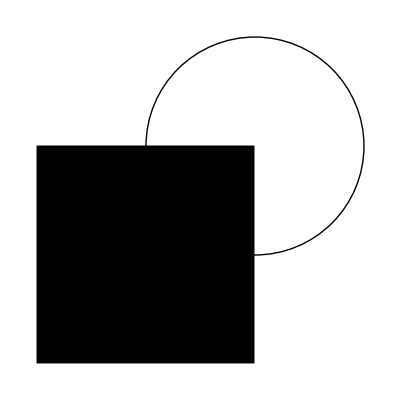

```mathematica
Graphics[{
Circle[{1,1},1],
Rectangle[{-1,-1},{1,1}],
}]
```

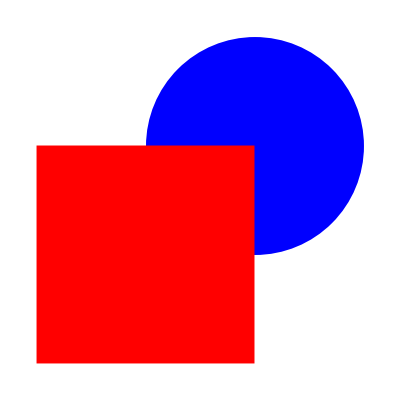

```mathematica
Graphics[{
Blue,Disk[{1,1},1],
Red,
Rectangle[{-1,-1},{1,1}],
}]
```

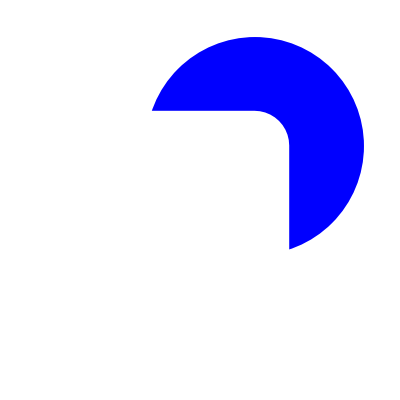

```mathematica
Graphics[{
Blue,Disk[{1,1},1],
White,EdgeForm[Directive[Thickness[.5],Dashed]],
Rectangle[{-1,-1},{1,1}],
}]
```

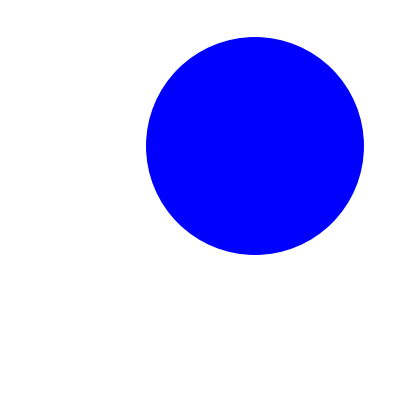

```mathematica
Graphics[{
White,EdgeForm[Directive[Thickness[.005],Dashed]],
Rectangle[{-1,-1},{1,1}],
EdgeForm[None],
Blue,Disk[{1,1},1]
}]
```

```mathematica
Graphics[{
White,EdgeForm[Directive[Thickness[.005],Dashed]],
Rectangle[{-1,-1},{1,1}],
EdgeForm[None],
Blue,{{{Disk[.2{1,1},.05]}}},
Thickness[.01],
Arrow[{.2{1,1},{.3,.4}}]
}]
```

-Graphics-

# Цвета

```mathematica
Blue
```

RGBColor[0, 0, 1]

```mathematica
RGBColor[0, 0, 1]//FullForm
```

RGBColor[0,0,1]

```mathematica
RGBColor[.9,.2,.3]
```

RGBColor[0.9, 0.2, 0.3]

```mathematica
RGBColor[0.31, 0.77, 0.45]
```

RGBColor[0.31, 0.77, 0.45]

```mathematica
RGBColor[.9,.2,.3,.4]
```

RGBColor[0.9, 0.2, 0.3, 0.4]

```mathematica
ColorData[3]
```

ColorDataFunction[…]

```mathematica
ColorData[3][4]
```

RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862]

```mathematica
ColorData[3]/@Range[10]
```

{RGBColor[0., 0., 0.],RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.996078431372549, 0.9882352941176471, 0.03529411764705882],RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],RGBColor[0.1450980392156863, 0.43529411764705883, 0.3843137254901961],RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],RGBColor[0.15294117647058825, 0.11372549019607843, 0.49019607843137253],RGBColor[0.47058823529411764, 0.2627450980392157, 0.5843137254901961],RGBColor[0.8901960784313725, 0.011764705882352941, 0.49019607843137253],RGBColor[0.9058823529411765, 0.027450980392156862, 0.12941176470588237]}

```mathematica
ColorData/@Range[8]
```

{ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…]}

# Задача

```mathematica
(Flatten[{RandomReal[{-1,1},4],ColorData[3][#]}]&/@Range[8])
```

{{-0.755888,0.969415,0.232613,-0.810135,RGBColor[0., 0., 0.]},{0.0697005,-0.915704,-0.0197519,-0.648394,RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862]},{0.630061,-0.219442,0.152534,-0.502579,RGBColor[0.996078431372549, 0.9882352941176471, 0.03529411764705882]},{-0.687268,-0.876847,0.696427,0.114215,RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862]},{-0.169385,-0.566104,0.707201,0.644766,RGBColor[0.1450980392156863, 0.43529411764705883, 0.3843137254901961]},{-0.136515,-0.727695,-0.587773,-0.785913,RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824]},{-0.83959,-0.448895,0.81154,0.853577,RGBColor[0.15294117647058825, 0.11372549019607843, 0.49019607843137253]},{-0.84303,0.646506,0.00100485,-0.358778,RGBColor[0.47058823529411764, 0.2627450980392157, 0.5843137254901961]}}

```mathematica
G[x_,y_,vx_,vy_,col_]:=
Module[{x1,y1},
{x1,y1}={x,y}+.2{vx,vy};
{col,EdgeForm[None],Disk[{x,y},.035],
Thickness[0.01],Arrow[{{x,y},{x1,y1}}]}
];
```

```mathematica
G@@Flatten[{RandomReal[{-1,1},4],ColorData[3][4]}]
```

{RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],EdgeForm[None],Disk[{0.435571,-0.779554},0.035],Thickness[0.01],Arrow[{{0.435571,-0.779554},{0.440272,-0.974175}}]}

@@@ ≈ /@ + @@ (Map[]+ Apply[])

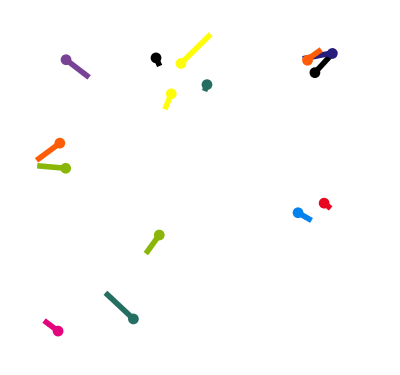

```mathematica
Graphics[{
White,EdgeForm[Directive[Thickness[0.005],Dashed]],
Rectangle[{-1,-1},{1,1}],
EdgeForm[None],Thickness[.01],

G@@@(Flatten[{RandomReal[{-1,1},4],ColorData[3][#]}]&/@Range[15])

}]
```

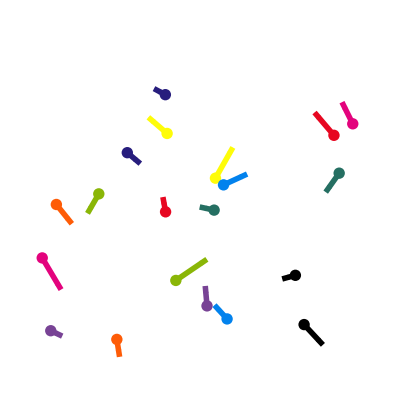

```mathematica
SeedRandom[1];
Graphics[{
White,EdgeForm[Directive[Thickness[.005],Dashed]],
Rectangle[{-1,-1},{1,1}],
EdgeForm[None],
Thickness[.01],
{#5,Disk[{#1,#2},.035],Arrow[{{#1,#2},{#1,#2}+.2{#3,#4}}]}&@@Flatten[{RandomReal[{-1,1},4],ColorData[3][#]}]&/@Range[20]
}]
```

```mathematica
SeedRandom[1];
ic=Flatten[{(RandomReal[{-1,1},4]),ColorData[3][#]}]&/@Range[20];

pic0[t_]:=Graphics[{
White,EdgeForm[Directive[Thickness[.005],Dashed]],
Rectangle[{-1,-1},{1,1}],
EdgeForm[None],
Thickness[.01],
{#5,Disk[{TriangleWave[(#1+#3 t)/4],TriangleWave[(#2+#4 t)/4]},.035]}&@@@ic
},PlotRange->1.05{{-1,1},{-1,1}}]

Animate[pic0[t],{t,0,10}]
```

```mathematica
Clear[t];
pic1[t_]=Graphics[{
White,EdgeForm[Directive[Thickness[.005],Dashed]],
Rectangle[{-1,-1},{1,1}],
EdgeForm[None],
Thickness[.01],
Function[{x,y,vx,vy,col},{col,Disk[{x,y},.035],Arrow[{{x,y},{x,y}+.2{vx,vy}}]}]@@@({TriangleWave[(#1+t#3)/4],TriangleWave[(#2+t#4)/4],D[TriangleWave[(#1+t1#3)/4],t1]/.t1->t,D[TriangleWave[(#2+t1#4)/4],t1]/.t1->t,#5}&@@@(Flatten[{RandomReal[{-1,1},4],ColorData[3][#]}]&/@Range[20]))
},PlotRange->1.1{{-1,1},{-1,1}}];

Animate[pic1[t],{t,0,10}]
```

# Графики



```mathematica
Plot[Sin[x],{x,0,10}]
```

```mathematica
Plot[Sin[x],{x,0,10}]//FullForm
```

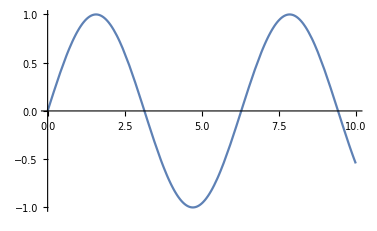
```mathematica
-Graphics-/.Line->Point
```

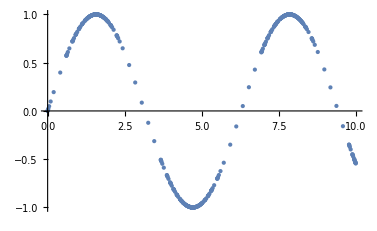

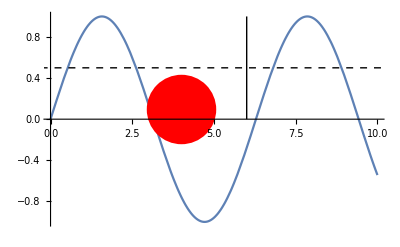

```mathematica
Plot[Sin[x],{x,0,10},Epilog->{Red,PointSize[.2],Point[{4,.1}],
Black,Line[{{6,0},{6,1}}],
Dashed,InfiniteLine[{0,.5},{1,0}]
}]
```

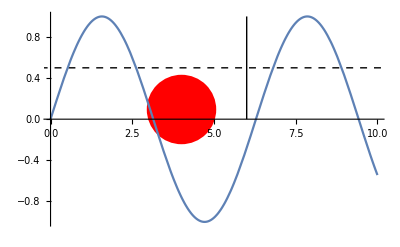

```mathematica
Plot[Sin[x],{x,0,10},Prolog->{Red,PointSize[.2],Point[{4,.1}],
Black,Line[{{6,0},{6,1}}],
Dashed,InfiniteLine[{0,.5},{1,0}]
},Method->{"AxesInFront" -> False}]
```

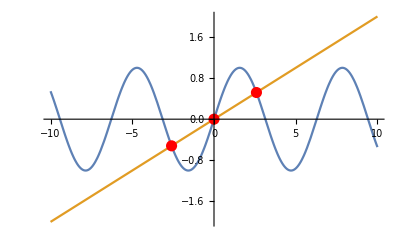

```mathematica
f1[x_]:=Sin[x];f2[x_]:=x/5;

sol=NSolve[f1[x]==f2[x],x,Reals];
list={x,f1[x]}/.sol;

Plot[{f1[x],f2[x]},{x,-10,10},PlotRange->{{-10,10},{-2,2}},Epilog->{Red,PointSize[.02],Point/@list}]
```

# Задача 3.3

```mathematica
F[r_]:=-1/r+1/r^2;
T=100;

sol=NDSolve[{
x''[t]==F[r] x[t]/r,y''[t]==F[r]y[t]/r,
x[0]==0,x'[0]==3/2,
y[0]==1,y'[0]==0
}/.r->√(x[t]^2+y[t]^2),{x,y},{t,0,T}]⟦1⟧;
```

```mathematica
Animate[
ParametricPlot[{x[t],y[t]}/.sol,{t,0,t1},PlotRange->8{{-1,1},{-1,1}}],
{t1,0.001,T}]
```

# Анимация

```mathematica
Graphics[{
Disk[{x[t],y[t]},.1]/.sol/.t->2
}
,PlotRange->8{{-1,1},{-1,1}}]
```

-Graphics-

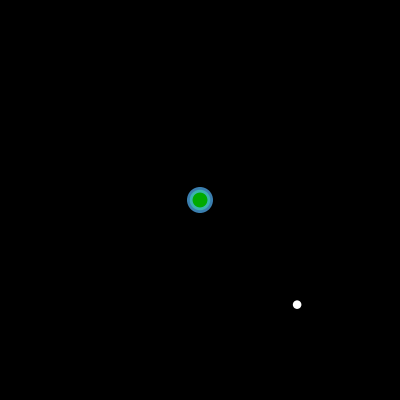

```mathematica
pic2[t_]:=Graphics[{Darker[Green],EdgeForm[Directive[RGBColor[Rational[1, 3], 0.72, 1, 0.6900000000000001],Thickness[.01]]],Disk[{0,0},.5],
White,EdgeForm[None],Disk[{x[t],y[t]},.21]/.sol
}
,PlotRange->8{{-1,1},{-1,1}},Background->Black];

pic2[T/2]
```

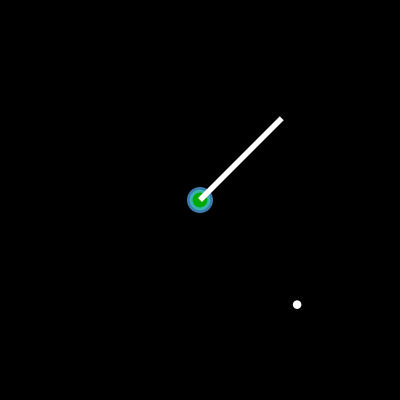

```mathematica
pic2[t_]:=Graphics[{Darker[Green],EdgeForm[Directive[RGBColor[Rational[1, 3], 0.72, 1, 0.6900000000000001],Thickness[.01]]],Disk[{0,0},.5],
White,Thickness[.01],Line[{{0,0},{4,4}}],
EdgeForm[None],Disk[{x[t],y[t]},.21]/.sol
}
,PlotRange->8{{-1,1},{-1,1}},Background->Black];

pic2[T/2]
```

```mathematica
pic2[t_]:=Graphics[{Darker[Green],EdgeForm[Directive[RGBColor[Rational[1, 3], 0.72, 1, 0.6900000000000001],Thickness[.01]]],Disk[{0,0},.5],
White,Thickness[.01],Line[{x[#],y[#]}/.sol&/@Subdivide[Max[t-10,0],t,100]],
EdgeForm[None],Disk[{x[t],y[t]},.21]/.sol
}
,PlotRange->8{{-1,1},{-1,1}},Background->Black];

Animate[pic2[t],{t,0,T}]
```

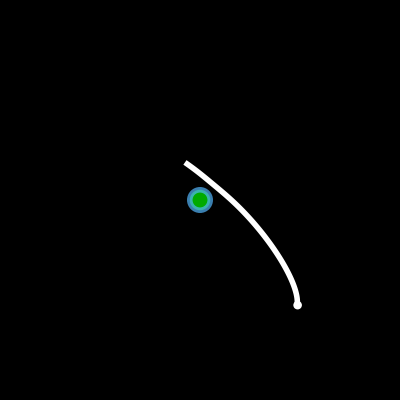

```mathematica
np=100;
pic3[t_]:=Graphics[{Darker[Green],EdgeForm[Directive[RGBColor[Rational[1, 3], 0.72, 1, 0.6900000000000001],Thickness[.01]]],Disk[{0,0},.5],
White,Thickness[.01],Line[{x[#],y[#]}/.sol&/@Subdivide[Max[t-10,0],t,np],VertexColors->(Opacity[#,White]&/@Subdivide[0,1,np])],
EdgeForm[None],Disk[{x[t],y[t]},.21]/.sol
}
,PlotRange->8{{-1,1},{-1,1}},Background->Black];

img=pic3[T/2]
```

# Экспорт

```mathematica
Directory[]
```

```mathematica
NotebookDirectory[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

```mathematica
Directory[]
```

```mathematica
FileNames[]
```

```mathematica
Export["pic.pdf",img,"pdf"]
```

pic.pdf

```mathematica
Export["pic.png",img,"png"]
```

pic.png

```mathematica
Export["pic.png",img,"png",ImageSize->1000]
```

pic.png

## !

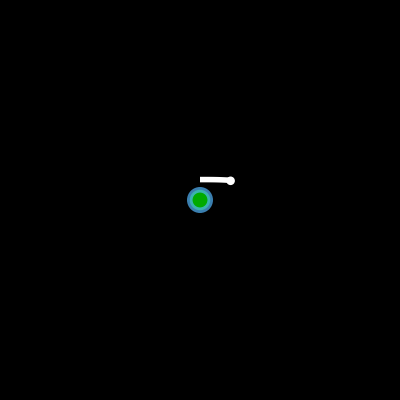

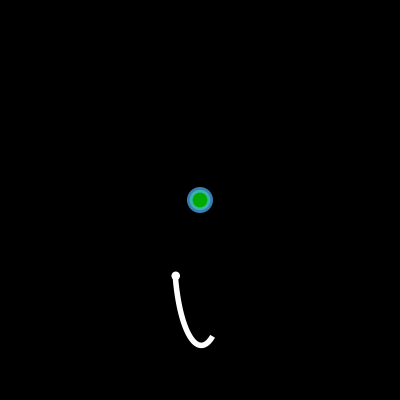

```mathematica
Pic[t_]:=pic3[t T];
pic3[1]
Pic[1]
```

```mathematica
(*Параметры анимации:*) 
dirname="animation_frames"; (*имя анимации*)
size=250; (*разрешение кадра в пикселях*)
time=5; (*время анимации в секундах*)
fps=25; (*частота кадров*)
loop=False;(*зациклевание анимации*)

(*Покадровый экспорт в .png:*) 
Nframes=Ceiling[fps time]; (*количество кадров*)
SetDirectory@NotebookDirectory[];
Quiet@CreateDirectory[dirname]; (*создание папки для сохранения кадров*)
Export[
dirname<>"//frame"<>StringPadLeft[ToString[#-1],4,"0"]<>".png",Rasterize[Pic[(#-1)/(Nframes-Boole[!loop])],ImageSize->size],"png"]&/@Range[Nframes];
```